```mathematica
ClearAll[c,G,MSun,rhoRadBBN];

c=29979245800;                   (*velocidad de la luz:cm/s*)
G=66743/10^12;                   (*constante gravitacional:cm^3/(g s^2)*)
MSun=198847*10^28;               (*masa solar:g*)

rhoRadBBN=7331305019814086*10^11;
(*densidad de energía de radiación en BBN:erg/cm^3*)
```

```mathematica
ti=37/50;                       (*coordenada temporal de BBN:0.74 s*)
ai=83/500000000000;             (*factor de escala en BBN:1.66*10^-10*)
Hti=67/100;                     (*parámetro de Hubble en BBN:0.67 s^-1*)
```

```mathematica
ρ0[ξ_]:= ξ*rhoRadBBN
```

```mathematica
Cxi[ξ_]:= (4π G)/(3c^2)*ρ0[ξ]
```

```mathematica
ClearAll[sol];
```

```mathematica
tMin=-5;
(* n = -2 luego 
(Y[t])^((n-1)/2) ----> Y^(-3/2)
*)
```

```mathematica
ClearAll[sol,tBounce]
```

```mathematica
sol[ξ_]:=sol[ξ]=Quiet@NDSolve[{Y'[t]==v[t],v'[t]==2*Cxi[ξ]*(Y[t])^(-3/2),Y[ti]==1,v[ti]==2*Hti,WhenEvent[v[t]==0,"StopIntegration"]},{Y,v},{t,-1,ti},WorkingPrecision->40,AccuracyGoal->20,PrecisionGoal->20,Method->"StiffnessSwitching",MaxSteps->Infinity];
```

```mathematica
tBounce[ξ_]:=tBounce[ξ]=(Y/. sol[ξ][[1]])["Domain"][[1,1]];
```

```mathematica
tB= tBounce[1/10]
```

-0.04804588983848337271227326175715118010918

```mathematica
Yfunc[ξ_,t_]:=Y[t]/. sol[ξ][[1]];
vFunc[ξ_,t_]:=v[t]/. sol[ξ][[1]];
```

```mathematica
apos[ξ_,t_]:=ai*Sqrt[Yfunc[ξ,Abs[t]+tBounce[ξ]]];
```

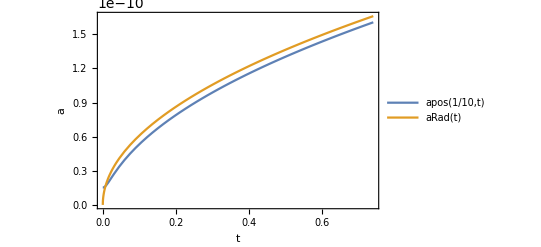

```mathematica
ar := ai/ti^(1/2)
aRad[t_]:= ar*t^(1/2)
Plot[{apos[1/10, t],aRad[t]},{t,0,ti},AxesLabel->{"t","a"},Frame->True,PlotRangePadding->0, PlotLegends->"Expressions"]
```

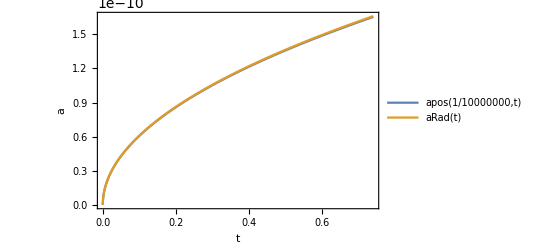

```mathematica
Plot[{apos[1/10000000, t],aRad[t]},{t,0,ti},AxesLabel->{"t","a"},Frame->True,PlotRangePadding->0, PlotLegends->"Expressions"]
```

```mathematica
ρbh[ξ_,t_]:= ρ0[ξ]*(ai/apos[ξ, t])^4
```

```mathematica
ρbh[1/10,0]
```

1.0130392752030331128731602033085485979×10^30

```mathematica
ρbh[1/10, 10^(-4)]
```

1.0129694673312664704043309649528882123×10^30

```mathematica
DotA[ξ_,t_]:=Sign[t]*(ai^2*vFunc[ξ,Abs[t]+tBounce[ξ]])/(2*apos[ξ,t]);
```

```mathematica
DotA[1/10, 0]
```

0

```mathematica
ρrad[ξ_, t_]:= (3c^2)/(8π G)(DotA[ξ, t]/apos[ξ, t])^2 -ρbh[ξ, t]
```

```mathematica
ρrad[1/10, 10^(-4)]
```

-1.0127818718219091677716726112385091139×10^30

```mathematica
ρrad[1/10, 0]
```

-1.0130392752030331128731602033085485979×10^30

```mathematica
HubbleParameter[ξ_, t_]:= √((8π G)/(3c^2)(ρrad[ξ, t]+ρbh[ξ, t]))
```

```mathematica
HubbleParameter[1/10, 0]
```

0.

```mathematica
HubbleParameter[1/10, 10^(-4)]
```

0.3416273879668079985207555732126836

```mathematica
5289.5069196841113186285097189208109531727050978632872936576626`36.94221135751255/5000
```

1.05790138393682226372570194378416219

```mathematica
MHubble[ξ_, t_]:= (4π c)/3*(ρrad[ξ, t]+ρbh[ξ, t])/(HubbleParameter[ξ, t])^3
```

```mathematica
γ := 0.2
Minic[ξ_, t_] := γ*MHubble[ξ, t]
```

```mathematica
Minic[1/10, 10^(-4)]
```

1.18169×10^38

```mathematica
Minic[1/10,10^(-4)]/MSun
```

59427.1

```mathematica
β = ρbh[1/10, 10^(-4)]/(ρrad[1/10, 10^(-4)]+ρbh[1/10, 10^(-4)])
```

5399.753281950477860628526569843217

```mathematica
xiCompareValues=10^-Range[10];
```

```mathematica
tForm=10^(-4);
```

```mathematica
tablaDatos=N[Table[{xi,HubbleParameter[xi,tForm],MHubble[xi,tForm],Minic[xi,tForm],Minic[xi,tForm]/MSun, ρbh[xi,tForm]/(ρrad[xi,tForm]+ρbh[xi,tForm])},{xi,xiCompareValues}],18];
```

```mathematica
Grid[Prepend[tablaDatos,{"ξ","H","\!\(\*SubscriptBox[\(M\), \(H\)]\)","\!\(\*SubscriptBox[\(M\), \(inic\)]\)","\!\(\*SubscriptBox[\(M\), \(inic\)]\)[MSun]", "β"}],Frame->All,Background->{None,{LightGray,None}},Alignment->Left]
```

ξ | H | M_H | M_inic | M_inic[MSun] | β
0.1 | 0.341627387966807999 | 5.90845196398927688×10^38 | 1.18169×10^38 | 59427.1 | 5399.75328195047786
0.01 | 1659.12255080852579 | 1.21660031105077841×10^35 | 2.4332×10^34 | 12.2365 | 0.110443809985258846
0.001 | 5280.09801512895528 | 3.82282488999537262×10^34 | 7.64565×10^33 | 3.84499 | 0.00111821656395804066
0.0001 | 5023.24513714153656 | 4.01829685049698538×10^34 | 8.03659×10^33 | 4.0416 | 0.000102497750574614754
0.00001 | 5002.21633188636376 | 4.03518935900125271×10^34 | 8.07038×10^33 | 4.05859 | 0.0000101693074840802644
1.×10^-6 | 5000.21972021317389 | 4.03680062943105893×10^34 | 8.0736×10^33 | 4.06021 | 1.01613704399892124×10^-6
1.×10^-7 | 5000.02194726233371 | 4.03696030272466782×10^34 | 8.07392×10^33 | 4.06037 | 1.01605770578271872×10^-7
1.×10^-8 | 5000.00219623215117 | 4.0369762495426202×10^34 | 8.07395×10^33 | 4.06038 | 1.01604977181540459×10^-8
1.×10^-9 | 5000.00021955727501 | 4.03697784550045574×10^34 | 8.07396×10^33 | 4.06039 | 1.01604897902665242×10^-9
1.×10^-10 | 5000.0000220665504 | 4.03697800495359103×10^34 | 8.07396×10^33 | 4.06039 | 1.01604889969440004×10^-10

```mathematica
formationHeaders = {"ξ", "H(t_form)","MHubble","Minic [g]", "Minic [Msun]", "β"};
```

```mathematica
csvPath=FileNameJoin[{NotebookDirectory[],"tabla_formacion_nm2.csv"}];
```

```mathematica
Export[csvPath,Prepend[tablaDatos,formationHeaders],"CSV"]
```

/home/iara/doctorado/tres incognitas/tabla_formacion_nm2.csv